```mathematica
littlewood[n_] := 1 + Tuples[{1,- 1}, n].x^Range[n]
```

```mathematica
littlewood[3]//Column//TraditionalForm
```

x^3+x^2+x+1
-x^3+x^2+x+1
x^3-x^2+x+1
-x^3-x^2+x+1
x^3+x^2-x+1
-x^3+x^2-x+1
x^3-x^2-x+1
-x^3-x^2-x+1

```mathematica
littlewoodRoots[n_]:= ComplexListPlot[x/. Solve[Times @@ littlewood[n]==0, x]]
```

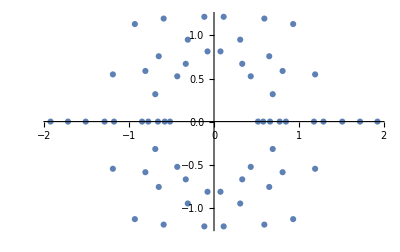

```mathematica
littlewoodRoots[4]
```

#### A fancier function with a slight increase in speed:

```mathematica
lwroots[n_Integer]:=List@@(#[[2]]&)/@Roots[#==0.,x]&/@littlewood[n]
```

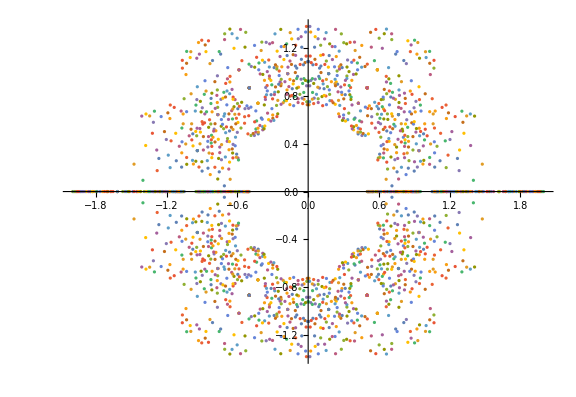

```mathematica
r=lwroots[8];
ComplexListPlot[r,ImageSize->Large,PlotStyle->PointSize[.004]]
```